```mathematica
Hpos[t_,tp_,m_,kap_,L_]:=ArrayFlatten[Table[(If[i<=L/2,m,m]*PauliMatrix[2]+kap*PauliMatrix[3])*KroneckerDelta[i,j]+.5*t*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+1,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-1,L,1]])+.5*tp*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+2,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-2,L,1]]),{i,1,L},{j,1,L}]]

Cpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2]))
Capos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[1;;L,1;;L]])
Cbpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[L+1;;2L,L+1;;2L]])
Cabpos[t_,tp_,m_,kap_,L_]:=(Cab = Cpos[t,tp,m,kap,L1];
Cab[[1;;L1,L1+1;;2L1]] = 0;
Cab[[L1+1;;2L1,1;;L1]] = 0; Cab)


Ck[t_,tp_,m_,kap_,k_]:=1/2(IdentityMatrix[2]-H[t,tp,m,kap,k]/Sqrt[-Det[H[t,tp,m,kap,k]]])
Caold[t_,tp_,m1_,kap_,L1_,ic_,fc_]:=Table[Sum[Exp[-I q1 (n-m)]*Ck[t,tp,m1,kap,q1]/L1,{q1,0,2Pi(1-1/L1),2Pi(1-1/L1)/(L1-1)}],{n,ic,fc},{m,ic,fc}];
Ca[t_,tp_,m_,kap_,L_,ic_,fc_]:=Sum[ArrayFlatten[ReleaseHold[DiagonalMatrix[Hold /@ ConstantArray[Sum[Exp[-I k1 (-l)]*Ck[t,tp,m,kap,k1]/L,{k1,0.0,0.0+2Pi(1-1/L1),2Pi(1-1/L1)/(L1-1)}],fc-ic+1-IntegerPart[Abs[l]]],IntegerPart[2l]] ]] ,{l,-fc+ic,fc-ic}];
Heval[t_,tp_,m_,kap_,L1_]:= Re[Eigenvalues[ArrayFlatten[Hpos[t,tp,m,kap,L1]]]];
ESeval2[t_,tp_,m_,kap_,L1_]:= Re[Eigenvalues[ArrayFlatten[Capos[t,tp,m,kap,L1]]]];
MatrixLogSafe[x_?(MatrixQ[#1,NumericQ]&)]:=MatrixLog[x+1.*^-9 IdentityMatrix[Length[x]]]/Log[2];
berryq1[t_,tp_,m_,kap_,k_,L1_]:=(Gqq =Table[ Ck[t,tp,m,kap,kt],{kt,k}];
egqq=Table[Eigenvectors[10*IdentityMatrix[2]+Gqq[[ki,;;,;;]]],{ki,1,L1}];
egqqOrd=Table[Map[Normalize[#/#[[1]]]&,egqq[[ki,;;,;;]]],{ki,1,L1}];
egqqOrd1 =Table[egqqOrd[[ki,;;,;;]][[1]],{ki,1,L1}];
inprod=Table[Conjugate[egqqOrd1 [[q1i,;;]]].egqqOrd1 [[q1i+1,;;]],{q1i,1,L1-1}];Mod[-Im[Log[Times@@inprod[[;;]]]],2Pi]/2/Pi)
berryq2[t_,tp_,m_,kap_,k_,L1_]:=(data =Table[Ck[t,tp,m,kap,ki],{ki,k}];Mod[-Im[Log[Tr[Dot @@ data ]]],2Pi]/2/Pi)
ct[a_,b_]:=Conjugate[{a}].Transpose[{b}]
c[a_,b_]:=a.b-b.a;
ac[a_,b_]:=a.b+b.a;
berryDisorder[t_, tp_, m_, kap_, L1_]:=(C2 =IdentityMatrix[2L1]*10+ Hpos[t,tp,m,kap,L1];
posop = KroneckerProduct[DiagonalMatrix[Table[i,{i,1,L1}]],IdentityMatrix[2]];
posoppbc = MatrixExp[-I 2Pi posop /(L1)];
vec = Orthogonalize[Eigenvectors[C2]];
S = Table[Conjugate[vec[[i,;;]]].posoppbc.vec[[j,;;]],{i,L1+1,2L1},{j,L1+1,2L1}];
-Im[Log[Det[S]]]/2/Pi+1/2
)
Essum[t_, tp_, m_, kap_, L1_]:=(Cab = Cpos[t,tp,m,kap,L1];
Cab[[1;;L1,L1+1;;2L1]] = 0;
Cab[[L1+1;;2L1,1;;L1]] = 0;
vecab = Orthogonalize[Eigenvectors[Cab]];
projl=DiagonalMatrix[Table[HeavisideTheta[L1/2+.1-i],{i,1,L1}
]];
projr=DiagonalMatrix[Table[HeavisideTheta[-L1/2-.1+i],{i,1,L1}
]];
projl2 = ArrayFlatten[{{projl-0*projr,ConstantArray[0,{L1,L1}]},{ConstantArray[0,{L1,L1}],projl-0*projr}}];
Sab=Table[Conjugate[vecab[[i,;;]]].MatrixExp[-I Pi projl2.Cab].vecab[[j,;;]],{i,L1+1,2L1},{j,L1+1,2L1}];
-Im[Log[Det[Sab.Inverse[Abs[Sab]]]]]/2/Pi
)
```

#### assymetric ES v Berry

```mathematica
L1=40; ic = 1; fc = L1/2;
t = 1.; tp =.2;m=0.;kap=0.301;
Ltp=40;
tplist=Table[tpi,{tpi,0,4,(4-0.01)/(Ltp-1)}];
k =  Table[q2,{q2,0.0,0.0+2Pi(1-1/L1),2Pi(1-1/L1)/(L1-1)}];
L1b=2000;
kb= Table[q2,{q2,0.0,0.0+2Pi(1-1/L1b),2Pi(1-1/L1b)/(L1b-1)}];
```

```mathematica
Hpos[t_,tp_,m_,kap_,L_]:=ArrayFlatten[Table[(If[i<=L/2,m,m]*PauliMatrix[2]+kap*Mod[(L-i-0),L]/L*PauliMatrix[3])*KroneckerDelta[i,j]+.5*If[i<=L/2,t,t]*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+1,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-1,L,1]])+.5*If[i<=L/2,tp,tp]*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+2,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-2,L,1]]),{i,1,L},{j,1,L}]]

Cpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2]))
Capos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[1;;L,1;;L]])
Cbpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[L+1;;2L,L+1;;2L]])
Cabpos[t_,tp_,m_,kap_,L_]:=(Cab = Cpos[t,tp,m,kap,L1];
Cab[[1;;L1,L1+1;;2L1]] = 0;
Cab[[L1+1;;2L1,1;;L1]] = 0; Cab)
```

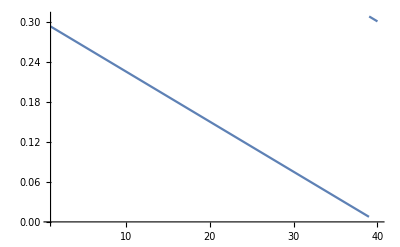

```mathematica
Plot[kap*Mod[(L1-i),L1,1]/L1,{i,1,L1}]
```

{2.85076,Null}

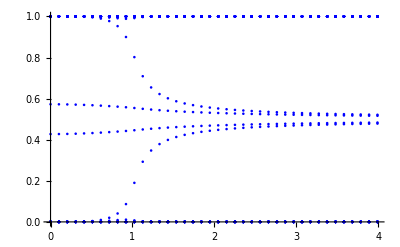

```mathematica
dataesa=Table[Transpose@{ConstantArray[tpi,L1],Re[Eigenvalues[Capos[t,tpi,m,kap,L1]]]},{tpi,tplist}];//AbsoluteTiming 
ListPlot[dataesa,PlotStyle->Blue]
```

{2.79781,Null}

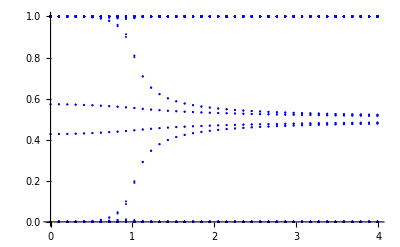

```mathematica
dataes=Table[Transpose@{ConstantArray[tpi,2L1],Re[Eigenvalues[Cabpos[t,tpi,m,kap,L1]]]},{tpi,tplist}];//AbsoluteTiming 
ListPlot[dataes,PlotStyle->Blue]
```

```mathematica
datavec=Table[Orthogonalize[Eigenvectors[Cabpos[t,tpi,m,kap,L1]]],{tpi,tplist}];
databerry=Table[berryDisorder[t,tpi,m,kap,L1],{tpi,tplist}];
signlr3=Table[If[Total[Abs[datavec[[m,i,1;;L1/2]]]^2]>.5,-1,If[Total[Abs[datavec[[m,i,L1+1;;3L1/2]]]^2]>.5,-1,1]],{m,1,Ltp},{i,1,2L1}];
```

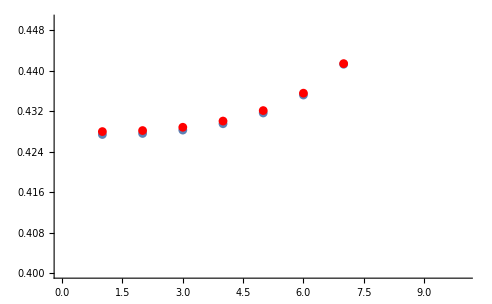

```mathematica
essum=Sum[-dataes[[;;,i,2]]*signlr3[[;;,i]]/2,{i,L1+1,2L1}];
Show[{ListPlot[Mod[essum,1],PlotRange->All],ListPlot[Mod[databerry,1],PlotStyle->Red]},PlotRange->{{0,10},{.4,.45}}]
```

#### assymetric ES v Berry shifted

```mathematica
L1=40; ic = 1; fc = L1/2;
t = 1.; tp =.2;m=0.;kap=0.301;
Ltp=41;
tplist=Table[tpi,{tpi,0,L1,(L1)/(Ltp-1)}];
k =  Table[q2,{q2,0.0,0.0+2Pi(1-1/L1),2Pi(1-1/L1)/(L1-1)}];
L1b=2000;
kb= Table[q2,{q2,0.0,0.0+2Pi(1-1/L1b),2Pi(1-1/L1b)/(L1b-1)}];
```

```mathematica
Hpos[t_,tp_,m_,kap_,L_]:=ArrayFlatten[Table[(If[i<=L/2,m,m]*PauliMatrix[2]+kap*Mod[(L-i-tp),L]/L*PauliMatrix[3])*KroneckerDelta[i,j]+.5*If[i<=L/2,t,t]*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+1,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-1,L,1]])+.5*0*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+2,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-2,L,1]]),{i,1,L},{j,1,L}]]

Cpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2]))
Capos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[1;;L,1;;L]])
Cbpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[L+1;;2L,L+1;;2L]])
Cabpos[t_,tp_,m_,kap_,L_]:=(Cab = Cpos[t,tp,m,kap,L1];
Cab[[1;;L1,L1+1;;2L1]] = 0;
Cab[[L1+1;;2L1,1;;L1]] = 0; Cab)
```

{2.60677,Null}

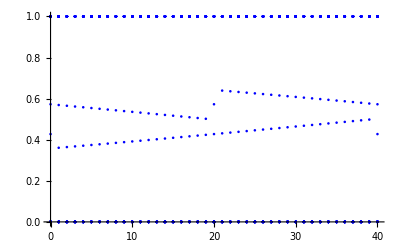

```mathematica
dataesa=Table[Transpose@{ConstantArray[tpi,L1],Re[Eigenvalues[Capos[t,tpi,m,kap,L1]]]},{tpi,tplist}];//AbsoluteTiming 
ListPlot[dataesa,PlotStyle->Blue]
```

{2.63335,Null}

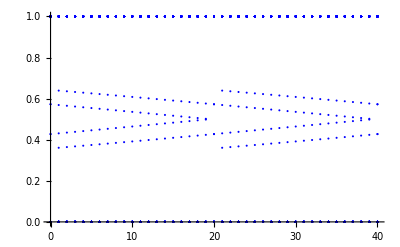

```mathematica
dataes=Table[Transpose@{ConstantArray[tpi,2L1],Re[Eigenvalues[Cabpos[t,tpi,m,kap,L1]]]},{tpi,tplist}];//AbsoluteTiming 
ListPlot[dataes,PlotStyle->Blue]
```

```mathematica
datavec=Table[Orthogonalize[Eigenvectors[Cabpos[t,tpi,m,kap,L1]]],{tpi,tplist}];
databerry=Table[berryDisorder[t,tpi,m,kap,L1],{tpi,tplist}];
signlr3=Table[If[Total[Abs[datavec[[m,i,1;;L1/2]]]^2]>.5,-1,If[Total[Abs[datavec[[m,i,L1+1;;3L1/2]]]^2]>.5,-1,1]],{m,1,Ltp},{i,1,2L1}];
```

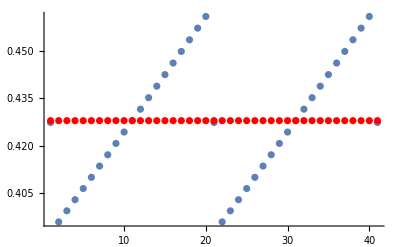

```mathematica
essum=Sum[-dataes[[;;,i,2]]*signlr3[[;;,i]]/2,{i,L1+1,2L1}];
Show[{ListPlot[Mod[essum,1],PlotRange->All],ListPlot[Mod[databerry,1],PlotStyle->Red]},PlotRange->All]
```

```mathematica
Total[essum]/41
```

0.42811

```mathematica
databerry[[1]]
```

0.427985

#### assymetric ES v Berry 21

```mathematica
L1=40; ic = 1; fc = L1/2;
t = 1.; tp =.2;m=0.;kap=0.301;
Ltp=40;
tplist=Table[tpi,{tpi,0,4,(4-0.01)/(Ltp-1)}];
k =  Table[q2,{q2,0.0,0.0+2Pi(1-1/L1),2Pi(1-1/L1)/(L1-1)}];
L1b=2000;
kb= Table[q2,{q2,0.0,0.0+2Pi(1-1/L1b),2Pi(1-1/L1b)/(L1b-1)}];
```

```mathematica
Hpos[t_,tp_,m_,kap_,L_]:=ArrayFlatten[Table[(If[i<=L/2,m,m]*PauliMatrix[2]+kap*Mod[(L-i-21),L]/L*PauliMatrix[3])*KroneckerDelta[i,j]+.5*If[i<=L/2,t,t]*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+1,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-1,L,1]])+.5*If[i<=L/2,tp,tp]*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+2,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-2,L,1]]),{i,1,L},{j,1,L}]]

Cpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2]))
Capos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[1;;L,1;;L]])
Cbpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[L+1;;2L,L+1;;2L]])
Cabpos[t_,tp_,m_,kap_,L_]:=(Cab = Cpos[t,tp,m,kap,L1];
Cab[[1;;L1,L1+1;;2L1]] = 0;
Cab[[L1+1;;2L1,1;;L1]] = 0; Cab)
```

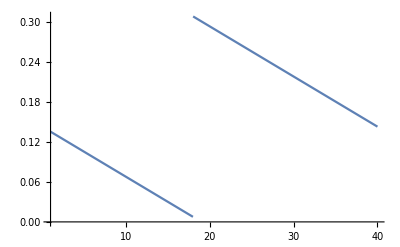

```mathematica
Plot[kap*Mod[(L1-i-21),L1,1]/L1,{i,1,L1}]
```

{2.74308,Null}

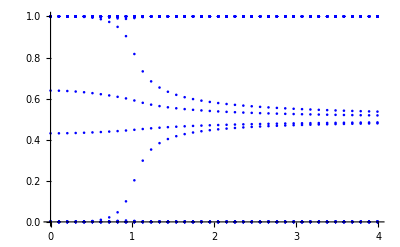

```mathematica
dataesa=Table[Transpose@{ConstantArray[tpi,L1],Re[Eigenvalues[Capos[t,tpi,m,kap,L1]]]},{tpi,tplist}];//AbsoluteTiming 
ListPlot[dataesa,PlotStyle->Blue]
```

{2.90841,Null}

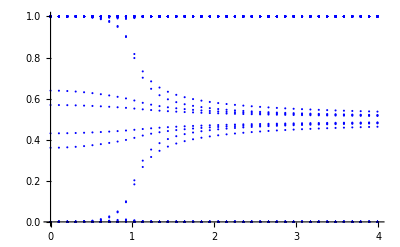

```mathematica
dataes=Table[Transpose@{ConstantArray[tpi,2L1],Re[Eigenvalues[Cabpos[t,tpi,m,kap,L1]]]},{tpi,tplist}];//AbsoluteTiming 
ListPlot[dataes,PlotStyle->Blue]
```

```mathematica
datavec=Table[Orthogonalize[Eigenvectors[Cabpos[t,tpi,m,kap,L1]]],{tpi,tplist}];
databerry=Table[berryDisorder[t,tpi,m,kap,L1],{tpi,tplist}];
signlr3=Table[If[Total[Abs[datavec[[m,i,1;;L1/2]]]^2]>.5,-1,If[Total[Abs[datavec[[m,i,L1+1;;3L1/2]]]^2]>.5,-1,1]],{m,1,Ltp},{i,1,2L1}];
```

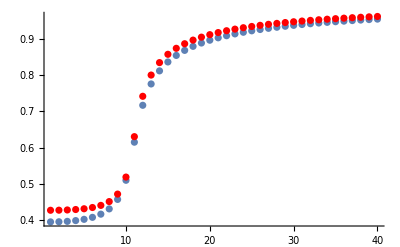

```mathematica
essum=Sum[-dataes[[;;,i,2]]*signlr3[[;;,i]]/2,{i,L1+1,2L1}];
Show[{ListPlot[Mod[essum,1],PlotRange->All],ListPlot[Mod[databerry,1],PlotStyle->Red]},PlotRange->All]
```

#### cos profile

```mathematica
L1=40; ic = 1; fc = L1/2;
t = 1.; tp =.2;m=0.;kap=0.301;
Ltp=40;
tplist=Table[tpi,{tpi,0,4,(4-0.01)/(Ltp-1)}];
k =  Table[q2,{q2,0.0,0.0+2Pi(1-1/L1),2Pi(1-1/L1)/(L1-1)}];
L1b=2000;
kb= Table[q2,{q2,0.0,0.0+2Pi(1-1/L1b),2Pi(1-1/L1b)/(L1b-1)}];
```

```mathematica
Hpos[t_,tp_,m_,kap_,L_]:=ArrayFlatten[Table[(If[i<=L/2,m,m]*PauliMatrix[2]+kap*Cos[2Pi*i/L]*PauliMatrix[3])*KroneckerDelta[i,j]+.5*If[i<=L/2,t,t]*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+1,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-1,L,1]])+.5*If[i<=L/2,tp,tp]*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+2,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-2,L,1]]),{i,1,L},{j,1,L}]]

Cpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2]))
Capos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[1;;L,1;;L]])
Cbpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[L+1;;2L,L+1;;2L]])
Cabpos[t_,tp_,m_,kap_,L_]:=(Cab = Cpos[t,tp,m,kap,L1];
Cab[[1;;L1,L1+1;;2L1]] = 0;
Cab[[L1+1;;2L1,1;;L1]] = 0; Cab)
```

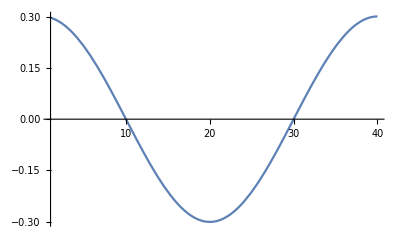

```mathematica
Plot[kap*Cos[2Pi(L1-i)/L1],{i,1,L1}]
```

{3.02667,Null}

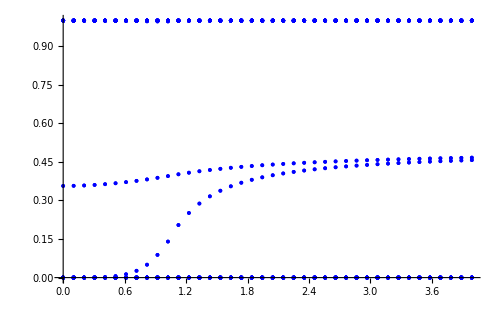

```mathematica
dataesa=Table[Transpose@{ConstantArray[tpi,L1],Re[Eigenvalues[Capos[t,tpi,m,kap,L1]]]},{tpi,tplist}];//AbsoluteTiming 
ListPlot[dataesa,PlotStyle->Blue]
```

{3.02964,Null}

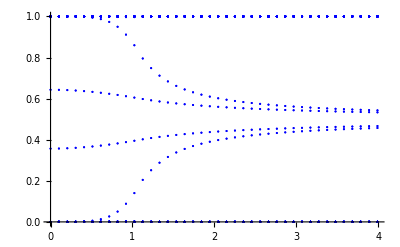

```mathematica
dataes=Table[Transpose@{ConstantArray[tpi,2L1],Re[Eigenvalues[Cabpos[t,tpi,m,kap,L1]]]},{tpi,tplist}];//AbsoluteTiming 
ListPlot[dataes,PlotStyle->Blue]
```

```mathematica
datavec=Table[Orthogonalize[Eigenvectors[Cabpos[t,tpi,m,kap,L1]]],{tpi,tplist}];
databerry=Table[berryDisorder[t,tpi,m,kap,L1],{tpi,tplist}];
signlr3=Table[If[Total[Abs[datavec[[m,i,1;;L1/2]]]^2]>.5,-1,If[Total[Abs[datavec[[m,i,L1+1;;3L1/2]]]^2]>.5,-1,1]],{m,1,Ltp},{i,1,2L1}];
```

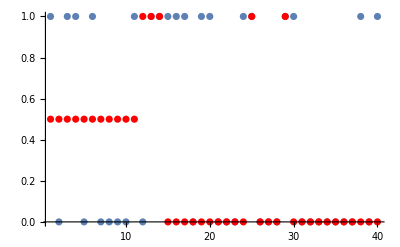

```mathematica
essum=Sum[-dataes[[;;,i,2]]*signlr3[[;;,i]]/2,{i,L1+1,2L1}];
Show[{ListPlot[Mod[essum,1],PlotRange->All],ListPlot[Mod[databerry,1],PlotStyle->Red]},PlotRange->All,DataRange->{0,tplist[[Ltp]]}]
```

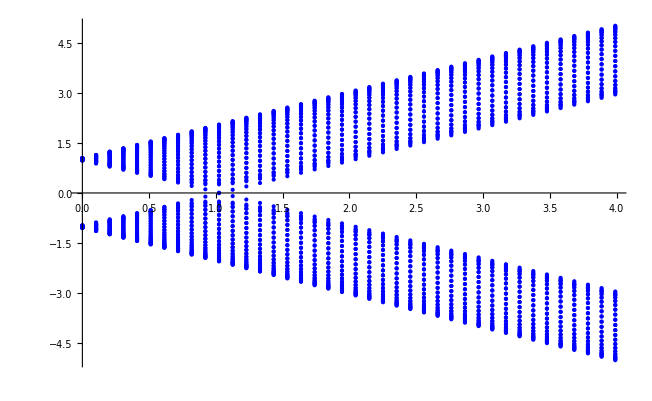

```mathematica
ListPlot[Table[Transpose@{ConstantArray[tpi,2L1],Re[Eigenvalues[Hpos[t,tpi,m,kap,L1]]]},{tpi,tplist}],PlotStyle->Blue]
```

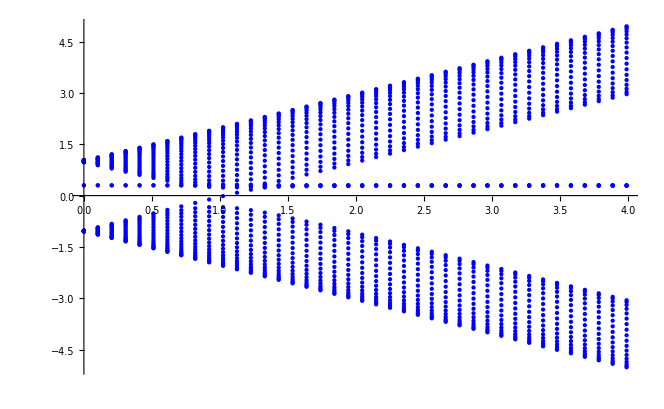

```mathematica
ListPlot[Table[Transpose@{ConstantArray[tpi,L1],Re[Eigenvalues[Hpos[t,tpi,m,kap,L1][[1;;L1,1;;L1]]]]},{tpi,tplist}],PlotStyle->Blue]
```

#### stepwise profile

```mathematica
L1=40; ic = 1; fc = L1/2;
t = 1.; tp =.2;m=0.;kap=.3;
Ltp=40;
tplist=Table[tpi,{tpi,0,4,(4-0.01)/(Ltp-1)}];
k =  Table[q2,{q2,0.0,0.0+2Pi(1-1/L1),2Pi(1-1/L1)/(L1-1)}];
L1b=2000;
kb= Table[q2,{q2,0.0,0.0+2Pi(1-1/L1b),2Pi(1-1/L1b)/(L1b-1)}];
```

```mathematica
Hpos[t_,tp_,m_,kap_,L_]:=ArrayFlatten[Table[(If[i<=L/2,m,m]*PauliMatrix[2]+If[i<L1*3/8&&i≥1*L1/8,kap,0.001]*PauliMatrix[3])*KroneckerDelta[i,j]+.5*If[i<=L/2,t,t]*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+1,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-1,L,1]])+.5*If[i<=L/2,tp,tp]*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+2,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-2,L,1]]),{i,1,L},{j,1,L}]]

Cpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2]))
Capos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[1;;L,1;;L]])
Cbpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[L+1;;2L,L+1;;2L]])
Cabpos[t_,tp_,m_,kap_,L_]:=(Cab = Cpos[t,tp,m,kap,L1];
Cab[[1;;L1,L1+1;;2L1]] = 0;
Cab[[L1+1;;2L1,1;;L1]] = 0; Cab)
```

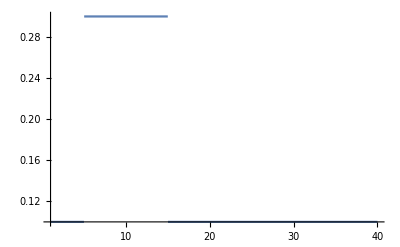

```mathematica
Plot[If[i<L1*3/8&&i≥ L1 1/8,kap,0.1],{i,1,L1}]
```

{2.73471,Null}

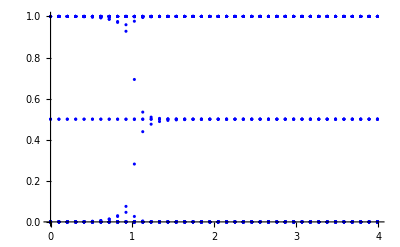

```mathematica
dataesa=Table[Transpose@{ConstantArray[tpi,L1],Re[Eigenvalues[Capos[t,tpi,m,kap,L1]]]},{tpi,tplist}];//AbsoluteTiming 
ListPlot[dataesa,PlotStyle->Blue]
```

{2.8643,Null}

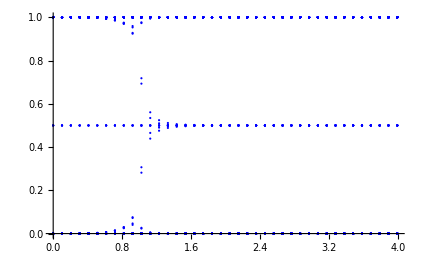

```mathematica
dataes=Table[Transpose@{ConstantArray[tpi,2L1],Re[Eigenvalues[Cabpos[t,tpi,m,kap,L1]]]},{tpi,tplist}];//AbsoluteTiming 
ListPlot[dataes,PlotStyle->Blue]
```

```mathematica
datavec=Table[Orthogonalize[Eigenvectors[Cabpos[t,tpi,m,kap,L1]]],{tpi,tplist}];
databerry2=Table[berryDisorder[t,tpi,m,kap,L1],{tpi,tplist}];
signlr3=Table[If[Total[Abs[datavec[[m,i,1;;L1/2]]]^2]>.5,-1,If[Total[Abs[datavec[[m,i,L1+1;;3L1/2]]]^2]>.5,-1,1]],{m,1,Ltp},{i,1,2L1}];
```

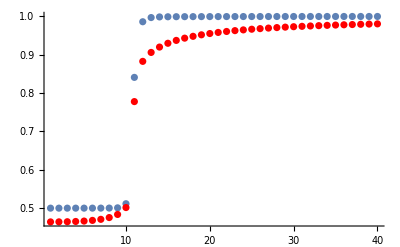

```mathematica
essum=Sum[-dataes[[;;,i,2]]*signlr3[[;;,i]]/2,{i,L1+1,2L1}];
Show[{ListPlot[Mod[essum,1],PlotRange->All],ListPlot[Mod[databerry,1],PlotStyle->Red]},PlotRange->All]
```

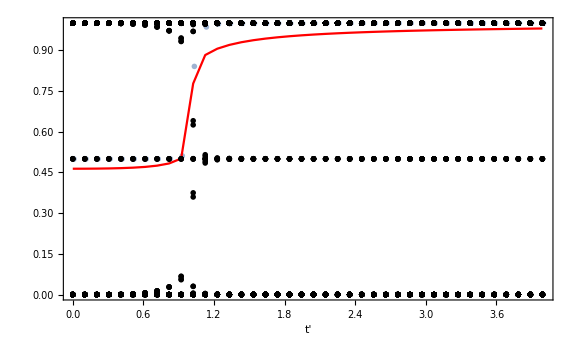

```mathematica
Show[{ListPlot[essum,PlotRange->All,DataRange->{0.01,4},PlotMarkers->{Automatic,Large},PlotStyle->Opacity[0.6]],ListPlot[databerry,DataRange->{0,tplist[[Ltp]]},PlotStyle->Red,Joined->True],ListPlot[dataes,PlotStyle->Black,PlotMarkers->{Graphics[Disk[{0,0},0.01]],.02}]},PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->Style["t'",16]]
```

#### stepwise profile 2

```mathematica
L1=40; ic = 1; fc = L1/2;
t = 1.; tp =.2;m=0.;kap=0.301;
Ltp=20;
tplist=Table[tpi,{tpi,0,4,(4-0.01)/(Ltp-1)}];
k =  Table[q2,{q2,0.0,0.0+2Pi(1-1/L1),2Pi(1-1/L1)/(L1-1)}];
L1b=2000;
kb= Table[q2,{q2,0.0,0.0+2Pi(1-1/L1b),2Pi(1-1/L1b)/(L1b-1)}];
```

```mathematica
Hpos[t_,tp_,m_,kap_,L_]:=ArrayFlatten[Table[(If[i<=L/2,m,m]*PauliMatrix[2]+If[i<L1*2/8&&i≥ 0*L1/8,kap,0.1]*PauliMatrix[3])*KroneckerDelta[i,j]+.5*If[i<=L/2,t,t]*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+1,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-1,L,1]])+.5*If[i<=L/2,tp,tp]*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+2,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-2,L,1]]),{i,1,L},{j,1,L}]]

Cpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2]))
Capos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[1;;L,1;;L]])
Cbpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[L+1;;2L,L+1;;2L]])
Cabpos[t_,tp_,m_,kap_,L_]:=(Cab = Cpos[t,tp,m,kap,L1];
Cab[[1;;L1,L1+1;;2L1]] = 0;
Cab[[L1+1;;2L1,1;;L1]] = 0; Cab)
```

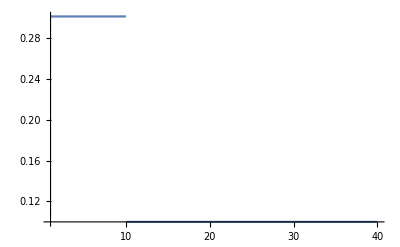

```mathematica
Plot[If[i<L1*2/8&&i≥ 0*L1/8,kap,0.1],{i,1,L1}]
```

{1.37005,Null}

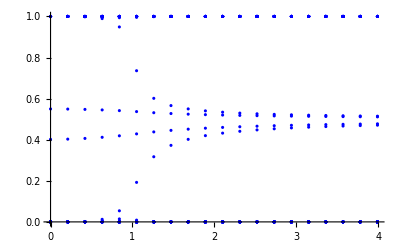

```mathematica
dataesa=Table[Transpose@{ConstantArray[tpi,L1],Re[Eigenvalues[Capos[t,tpi,m,kap,L1]]]},{tpi,tplist}];//AbsoluteTiming 
ListPlot[dataesa,PlotStyle->Blue]
```

{1.47002,Null}

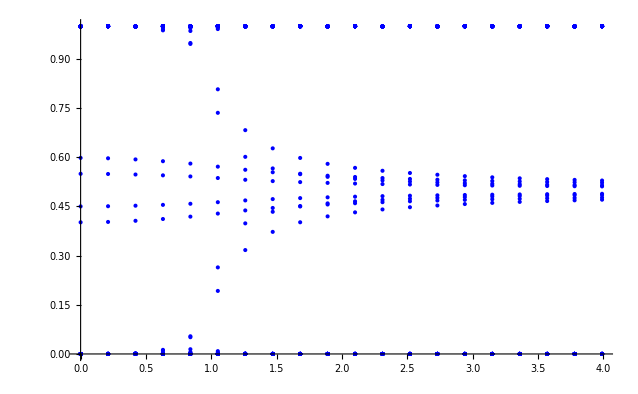

```mathematica
dataes=Table[Transpose@{ConstantArray[tpi,2L1],Re[Eigenvalues[Cabpos[t,tpi,m,kap,L1]]]},{tpi,tplist}];//AbsoluteTiming 
ListPlot[dataes,PlotStyle->Blue]
```

```mathematica
datavec=Table[Orthogonalize[Eigenvectors[Cabpos[t,tpi,m,kap,L1]]],{tpi,tplist}];
databerry=Table[berryDisorder[t,tpi,m,kap,L1],{tpi,tplist}];
signlr3=Table[If[Total[Abs[datavec[[m,i,1;;L1/2]]]^2]>.5,-1,If[Total[Abs[datavec[[m,i,L1+1;;3L1/2]]]^2]>.5,-1,1]],{m,1,Ltp},{i,1,2L1}];
```

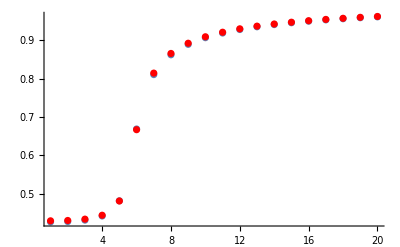

```mathematica
essum=Sum[-dataes[[;;,i,2]]*signlr3[[;;,i]]/2,{i,L1+1,2L1}];
Show[{ListPlot[Mod[essum,1],PlotRange->All],ListPlot[Mod[databerry,1],PlotStyle->Red]},PlotRange->All]
```

#### shift

```mathematica
L1=40; ic = 1; fc = L1/2;
t = 1.; tp =2.0;m=0.;kap=0.301;
Ltp=40;
tplist=Table[tpi,{tpi,1,L1}];
k =  Table[q2,{q2,0.0,0.0+2Pi(1-1/L1),2Pi(1-1/L1)/(L1-1)}];
L1b=2000;
kb= Table[q2,{q2,0.0,0.0+2Pi(1-1/L1b),2Pi(1-1/L1b)/(L1b-1)}];
```

```mathematica
Hpos[t_,tp_,m_,kap_,L_]:=(kapArray = ConstantArray[kap,L1];
kapArray[[L1/4+1;;L1]]  = .0001;
kapArray = RotateRight[kapArray,tp];ArrayFlatten[Table[(If[i<=L/2,m,m]*PauliMatrix[2]+kapArray[[i]]*PauliMatrix[3])*KroneckerDelta[i,j]+.5*If[i<=L/2,t,t]*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+1,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-1,L,1]])+.5*0*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+2,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-2,L,1]]),{i,1,L},{j,1,L}]])

Cpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2]))
Capos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[1;;L,1;;L]])
Cbpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[L+1;;2L,L+1;;2L]])
Cabpos[t_,tp_,m_,kap_,L_]:=(Cab = Cpos[t,tp,m,kap,L1];
Cab[[1;;L1,L1+1;;2L1]] = 0;
Cab[[L1+1;;2L1,1;;L1]] = 0; Cab)
```

{2.62548,Null}

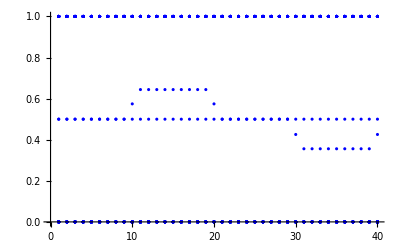

```mathematica
dataesa=Table[Transpose@{ConstantArray[tpi,L1],Re[Eigenvalues[Capos[t,tpi,m,kap,L1]]]},{tpi,tplist}];//AbsoluteTiming 
ListPlot[dataesa,PlotStyle->Blue]
```

{2.48281,Null}

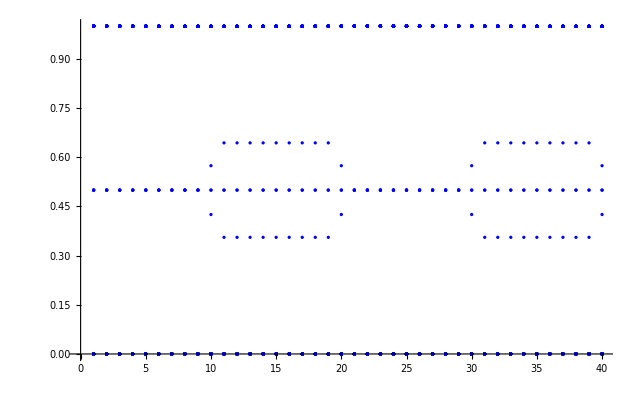

```mathematica
dataes=Table[Transpose@{ConstantArray[tpi,2L1],Re[Eigenvalues[Cabpos[t,tpi,m,kap,L1]]]},{tpi,tplist}];//AbsoluteTiming 
ListPlot[dataes,PlotStyle->Blue]
```

```mathematica
datavec=Table[Orthogonalize[Eigenvectors[Cabpos[t,tpi,m,kap,L1]]],{tpi,tplist}];
databerry=Table[berryDisorder[t,tpi,m,kap,L1],{tpi,tplist}];
signlr3=Table[If[Total[Abs[datavec[[m,i,1;;L1/2]]]^2]>.5,-1,If[Total[Abs[datavec[[m,i,L1+1;;3L1/2]]]^2]>.5,-1,1]],{m,1,Ltp},{i,1,2L1}];
```

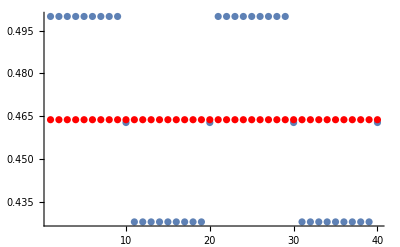

```mathematica
essum=Sum[-dataes[[;;,i,2]]*signlr3[[;;,i]]/2,{i,L1+1,2L1}];
Show[{ListPlot[Mod[essum,1],PlotRange->All],ListPlot[Mod[databerry,1],PlotStyle->Red]},PlotRange->All]
```

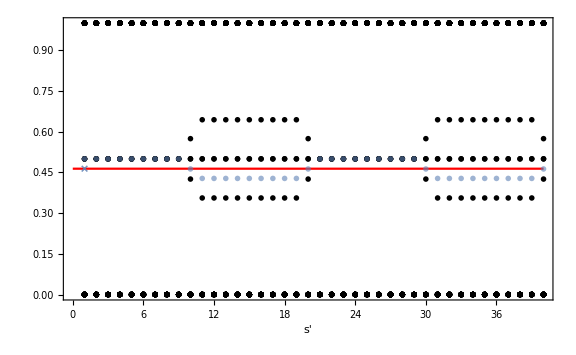

```mathematica
Show[{ListPlot[databerry,DataRange->{0,tplist[[Ltp]]},PlotStyle->Red,Joined->True],ListPlot[dataes,PlotStyle->Black,PlotMarkers->{Graphics[Disk[{0,0},0.01]],.02}],ListPlot[essum,DataRange->{1,40},PlotMarkers->{Automatic,Large},PlotStyle->Opacity[0.6]],ListPlot[{{1,Total[essum]/40}},PlotMarkers->{"×",Large},PlotStyle->{Opacity[0.6]}]},PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->Style["s'",16]]
```

```mathematica
×
```

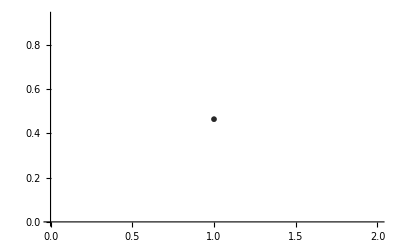

```mathematica
ListPlot[{{1,Total[essum]/40}},PlotMarkers->{Automatic,Large},PlotStyle->{Opacity[0.6],Black}]
```

```mathematica
Total[essum]/40
```

0.463816

```mathematica
databerry[[1]]
```

0.463748

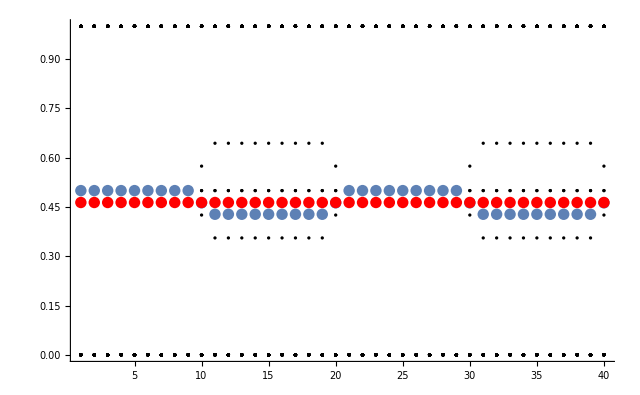

```mathematica
Show[{ListPlot[dataes,PlotStyle->Black] ,ListPlot[Mod[essum,1]],ListPlot[Mod[databerry,1],PlotStyle->Red]},PlotRange->All]
```

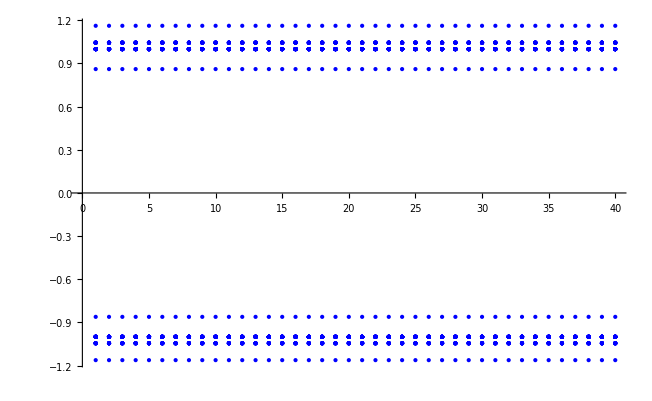

```mathematica
ListPlot[Table[Transpose@{ConstantArray[tpi,2L1],Re[Eigenvalues[Hpos[t,tpi,m,kap,L1]]]},{tpi,tplist}],PlotStyle->Blue]
```

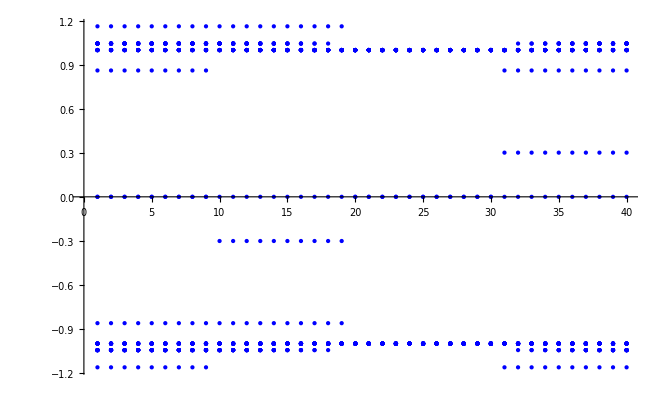

```mathematica
ListPlot[Table[Transpose@{ConstantArray[tpi,L1],Re[Eigenvalues[Hpos[t,tpi,m,kap,L1][[1;;L1,1;;L1]]]]},{tpi,tplist}],PlotStyle->Blue]
```

#### stepwise large shift

```mathematica
L1=40; ic = 1; fc = L1/2;
t = 1.; tp =.0;m=0.;kap=0.301;
Ltp=40;
tplist=Table[tpi,{tpi,1,L1}];
k =  Table[q2,{q2,0.0,0.0+2Pi(1-1/L1),2Pi(1-1/L1)/(L1-1)}];
L1b=2000;
kb= Table[q2,{q2,0.0,0.0+2Pi(1-1/L1b),2Pi(1-1/L1b)/(L1b-1)}];
```

```mathematica
Hpos[t_,tp_,m_,kap_,L_]:=(kapArray = ConstantArray[kap,L1];
kapArray[[3L1/4+1;;L1]]  = .0001;
kapArray = RotateRight[kapArray,tp];ArrayFlatten[Table[(If[i<=L/2,m,m]*PauliMatrix[2]+kapArray[[i]]*PauliMatrix[3])*KroneckerDelta[i,j]+.5*If[i<=L/2,t,t]*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+1,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-1,L,1]])+.0*If[i<=L/2,tp,tp]*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+2,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-2,L,1]]),{i,1,L},{j,1,L}]])

Cpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2]))
Capos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[1;;L,1;;L]])
Cbpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[L+1;;2L,L+1;;2L]])
Cabpos[t_,tp_,m_,kap_,L_]:=(Cab = Cpos[t,tp,m,kap,L1];
Cab[[1;;L1,L1+1;;2L1]] = 0;
Cab[[L1+1;;2L1,1;;L1]] = 0; Cab)
```

{2.47323,Null}

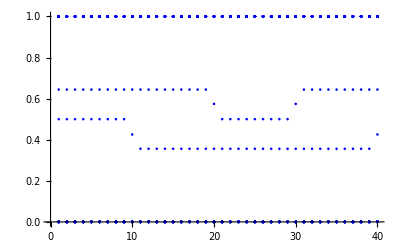

```mathematica
dataesa=Table[Transpose@{ConstantArray[tpi,L1],Re[Eigenvalues[Capos[t,tpi,m,kap,L1]]]},{tpi,tplist}];//AbsoluteTiming 
ListPlot[dataesa,PlotStyle->Blue]
```

{2.59639,Null}

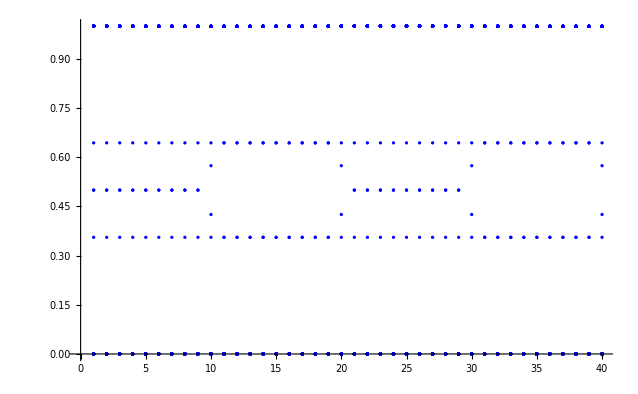

```mathematica
dataes=Table[Transpose@{ConstantArray[tpi,2L1],Re[Eigenvalues[Cabpos[t,tpi,m,kap,L1]]]},{tpi,tplist}];//AbsoluteTiming 
ListPlot[dataes,PlotStyle->Blue]
```

```mathematica
datavec=Table[Orthogonalize[Eigenvectors[Cabpos[t,tpi,m,kap,L1]]],{tpi,tplist}];
databerry=Table[berryDisorder[t,tpi,m,kap,L1],{tpi,tplist}];
signlr3=Table[If[Total[Abs[datavec[[m,i,1;;L1/2]]]^2]>.5,-1,If[Total[Abs[datavec[[m,i,L1+1;;3L1/2]]]^2]>.5,-1,1]],{m,1,Ltp},{i,1,2L1}];
```

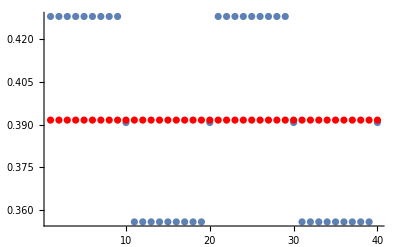

```mathematica
essum=Sum[-dataes[[;;,i,2]]*signlr3[[;;,i]]/2,{i,L1+1,2L1}];
Show[{ListPlot[Mod[essum,1],PlotRange->All],ListPlot[Mod[databerry,1],PlotStyle->Red]},PlotRange->All]
```

```mathematica
Total[essum]/40
```

0.391785

```mathematica
databerry[[1]]
```

0.463748

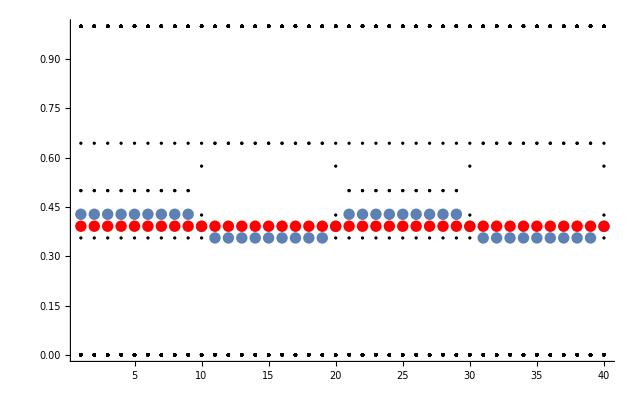

```mathematica
Show[{ListPlot[dataes,PlotStyle->Black] ,ListPlot[Mod[essum,1]],ListPlot[Mod[databerry,1],PlotStyle->Red]},PlotRange->All]
```

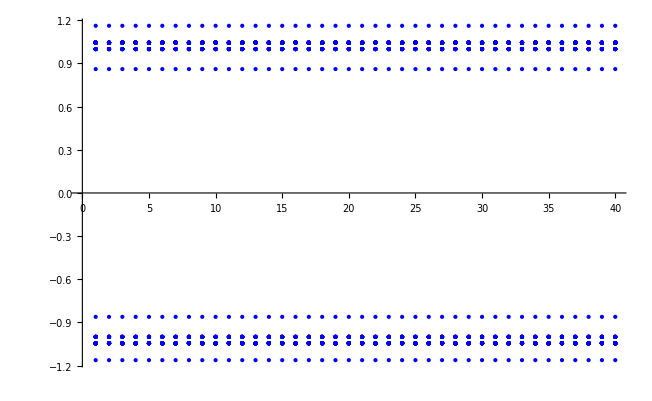

```mathematica
ListPlot[Table[Transpose@{ConstantArray[tpi,2L1],Re[Eigenvalues[Hpos[t,tpi,m,kap,L1]]]},{tpi,tplist}],PlotStyle->Blue]
```

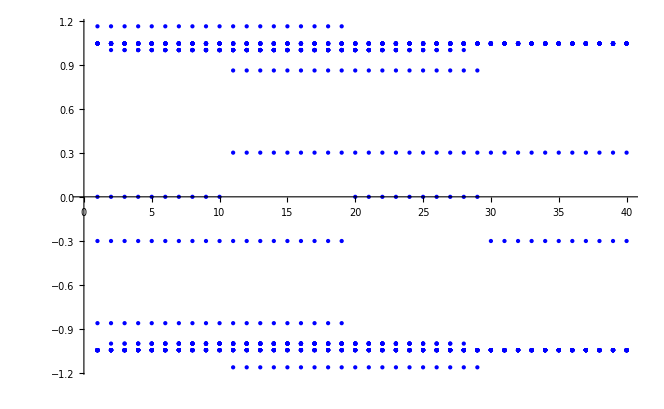

```mathematica
ListPlot[Table[Transpose@{ConstantArray[tpi,L1],Re[Eigenvalues[Hpos[t,tpi,m,kap,L1][[1;;L1,1;;L1]]]]},{tpi,tplist}],PlotStyle->Blue]
```

#### 10 full C_A

```mathematica
L1=40; ic = 1; fc = L1/2;
t = 1.; tp =.0;m=0.;kap=0.30;
Ltp=40;
tplist2=Table[tpi,{tpi,1,L1}];
tplist=Table[tpi,{tpi,0,2,2/(Ltp-1)}];
k =  Table[q2,{q2,0.0,0.0+2Pi(1-1/L1),2Pi(1-1/L1)/(L1-1)}];
L1b=2000;
kb= Table[q2,{q2,0.0,0.0+2Pi(1-1/L1b),2Pi(1-1/L1b)/(L1b-1)}];
```

```mathematica
Hpos[t_,tp_,m_,kap_,L_]:=(kapArray = ConstantArray[kap,L];
(*kapArray[[IntegerPart[L1/4]+1;;L1]]  = .000;*)
kapArray = RotateRight[kapArray,15];ArrayFlatten[Table[(m*PauliMatrix[2]+kapArray[[i]]*Cos[2 Pi i/L]*PauliMatrix[3])*KroneckerDelta[i,j]+.5*t*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+1,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-1,L,1]])+.5*tp*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+2,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-2,L,1]]),{i,1,L},{j,1,L}]])

Cpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2]))
Capos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[1;;L,1;;L]])
Cbpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[L+1;;2L,L+1;;2L]])
Cabpos[t_,tp_,m_,kap_,L_]:=(Cab = Cpos[t,tp,m,kap,L1];
Cab[[1;;L1,L1+1;;2L1]] = 0;
Cab[[L1+1;;2L1,1;;L1]] = 0; Cab)
```

{2.94574,Null}

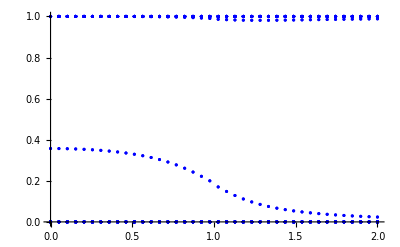

```mathematica
dataesa=Table[Transpose@{ConstantArray[tpi,L1],Re[Eigenvalues[Capos[t,0,tpi,kap,L1]]]},{tpi,tplist}];//AbsoluteTiming 
ListPlot[dataesa,PlotStyle->Blue]
```

```mathematica
datavec=Table[Orthogonalize[Eigenvectors[Capos[t,0,tpi,kap,L1]]],{tpi,tplist}];
databerry=Table[berryDisorder[t,0,tpi,kap,L1],{tpi,tplist}];
(*signlr3=Table[If[Total[Abs[datavec[[m,i,1;;L1/2]]]^2]>.5,-1,If[Total[Abs[datavec[[m,i,L1+1;;3L1/2]]]^2]>.5,-1,1]],{m,1,Ltp},{i,1,2L1}];*)
```

```mathematica
sign = Table[If[Total[Abs[datavec[[m,i,1;;L1/2]]]^2]>.5,-1,1],{m,1,Ltp},{i,1,L1}];
sign2 = -Table[Total[Abs[datavec[[m,i,1;;L1/2]]]^2]-Total[Abs[datavec[[m,i,L1/2+1;;L1]]]^2],{m,1,Ltp},{i,1,L1}];
sign3 = -Table[Abs[datavec[[m,i,1]]]^2-Abs[datavec[[m,i,L1]]]^2,{m,1,Ltp},{i,1,L1}];
```

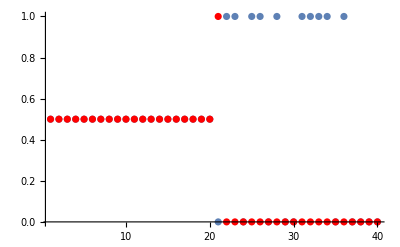

```mathematica
essum=Sum[-dataesa[[;;,i,2]]*sign[[;;,i]]/2,{i,1,L1}];
Show[{ListPlot[Mod[essum,1],PlotRange->All],ListPlot[Mod[databerry,1],PlotStyle->Red]},PlotRange->All]
```

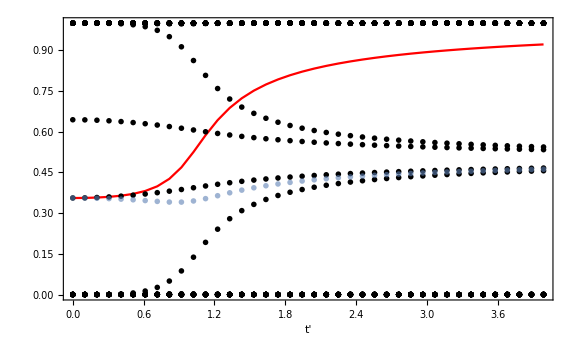

```mathematica
Show[{ListPlot[databerry,DataRange->{0,tplist[[Ltp]]},PlotStyle->Red,Joined->True],ListPlot[dataesa,PlotStyle->Black,PlotMarkers->{Graphics[Disk[{0,0},0.01]],.02}],ListPlot[Mod[essum,1],DataRange->{tplist[[1]],tplist[[Ltp]]},PlotMarkers->{Automatic,Large},PlotStyle->Opacity[0.6]]},PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->Style["t'",16],DataRange->{tplist[[1]],tplist[[Ltp]]}]
```

```mathematica
Mod[Total[Mod[essum,1]]/40,1]
```

0.463854

```mathematica
ListPlot[{{1,Total[essum]/40}},PlotMarkers->{Automatic,Large},PlotStyle->{Opacity[0.6],Black}]
```

-Graphics-

```mathematica
Total[essum]/40
```

0.463816

```mathematica
databerry[[1]]
```

0.463748

```mathematica
Show[{ListPlot[dataes,PlotStyle->Black] ,ListPlot[Mod[essum,1]],ListPlot[Mod[databerry,1],PlotStyle->Red]},PlotRange->All]
```

-Graphics-

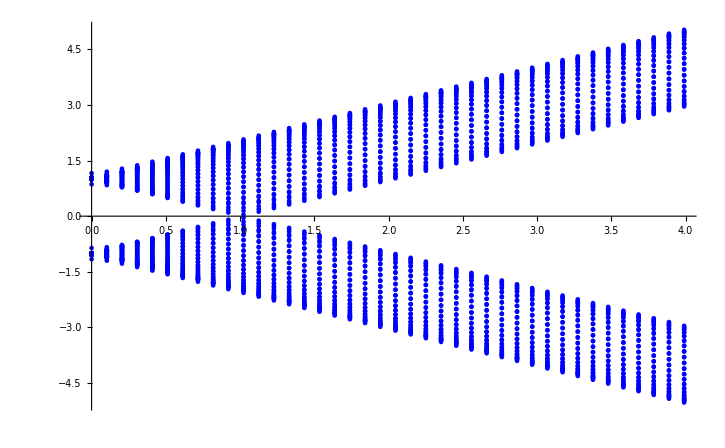

```mathematica
ListPlot[Table[Transpose@{ConstantArray[tpi,2L1],Re[Eigenvalues[Hpos[t,tpi,m,kap,L1]]]},{tpi,tplist}],PlotStyle->Blue]
```

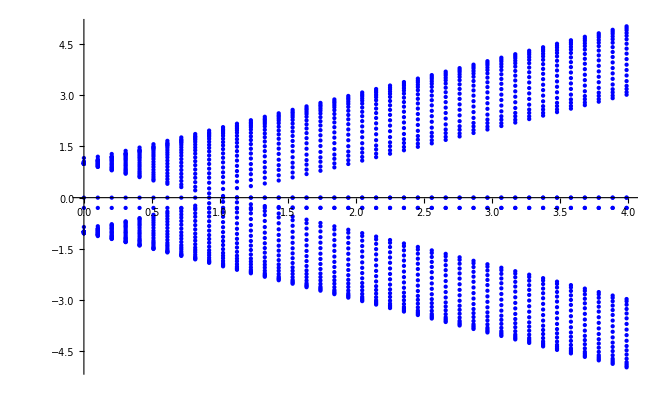

```mathematica
ListPlot[Table[Transpose@{ConstantArray[tpi,L1],Re[Eigenvalues[Hpos[t,tpi,m,kap,L1][[1;;L1,1;;L1]]]]},{tpi,tplist}],PlotStyle->Blue]
```

#### cos profile full C_A

```mathematica
L1=30; ic = 1; fc = L1/2;
t = 1.; tp =.2;m=0.;kap=0.301;
Ltp=40;
tplist=Table[tpi,{tpi,0,4,(4-0.01)/(Ltp-1)}];
k =  Table[q2,{q2,0.0,0.0+2Pi(1-1/L1),2Pi(1-1/L1)/(L1-1)}];
L1b=2000;
kb= Table[q2,{q2,0.0,0.0+2Pi(1-1/L1b),2Pi(1-1/L1b)/(L1b-1)}];
```

```mathematica
Hpos[t_,tp_,m_,kap_,L_]:=ArrayFlatten[Table[(If[i<=L/2,m,m]*PauliMatrix[2]+kap*Cos[2Pi*i/L]*PauliMatrix[3])*KroneckerDelta[i,j]+.5*If[i<=L/2,t,t]*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+1,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-1,L,1]])+.5*If[i<=L/2,tp,tp]*((PauliMatrix[1]+I PauliMatrix[2])KroneckerDelta[i,Mod[j+2,L,1]]+(PauliMatrix[1]-I PauliMatrix[2])KroneckerDelta[i,Mod[j-2,L,1]]),{i,1,L},{j,1,L}]]

Cpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2]))
Capos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[1;;L,1;;L]])
Cbpos[t_,tp_,m_,kap_,L_]:=(h=Hpos[t,tp,m,kap,L];1/2(IdentityMatrix[2L]-h.MatrixPower[h.h,-1/2])[[L+1;;2L,L+1;;2L]])
Cabpos[t_,tp_,m_,kap_,L_]:=(Cab = Cpos[t,tp,m,kap,L1];
Cab[[1;;L1,L1+1;;2L1]] = 0;
Cab[[L1+1;;2L1,1;;L1]] = 0; Cab)
```

```mathematica
Plot[kap*Cos[2Pi(L1-i)/L1],{i,1,L1}]
```

-Graphics-

{1.69226,Null}

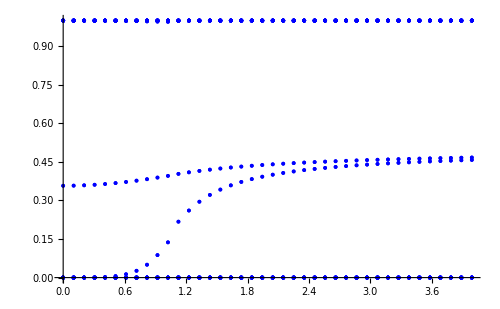

```mathematica
dataesa=Table[Transpose@{ConstantArray[tpi,L1],Re[Eigenvalues[Capos[t,tpi,m,kap,L1]]]},{tpi,tplist}];//AbsoluteTiming 
ListPlot[dataesa,PlotStyle->Blue]
```

```mathematica
dataes=Table[Transpose@{ConstantArray[tpi,2L1],Re[Eigenvalues[Cabpos[t,tpi,m,kap,L1]]]},{tpi,tplist}];//AbsoluteTiming 
ListPlot[dataes,PlotStyle->Blue]
```

{3.09603,Null}

-Graphics-

```mathematica
dataveca=Table[Orthogonalize[Eigenvectors[Capos[t,tpi,m,kap,L1]]],{tpi,tplist}];
databerry=Table[berryDisorder[t,tpi,m,kap,L1],{tpi,tplist}];
sign = Table[If[Total[Abs[dataveca[[m,i,1;;L1/2]]]^2]>.5,-1,1],{m,1,Ltp},{i,1,L1}];
```

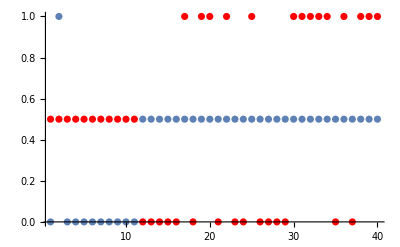

```mathematica
essuma=Sum[-dataesa[[;;,i,2]]*sign[[;;,i]]/2,{i,1,L1}];
Show[{ListPlot[Mod[essuma,1],PlotRange->All],ListPlot[Mod[databerry,1],PlotStyle->Red]},PlotRange->All]
```

```mathematica
ListPlot[Table[Transpose@{ConstantArray[tpi,2L1],Re[Eigenvalues[Hpos[t,tpi,m,kap,L1]]]},{tpi,tplist}],PlotStyle->Blue]
```

-Graphics-

```mathematica
ListPlot[Table[Transpose@{ConstantArray[tpi,L1],Re[Eigenvalues[Hpos[t,tpi,m,kap,L1][[1;;L1,1;;L1]]]]},{tpi,tplist}],PlotStyle->Blue]
```

-Graphics-